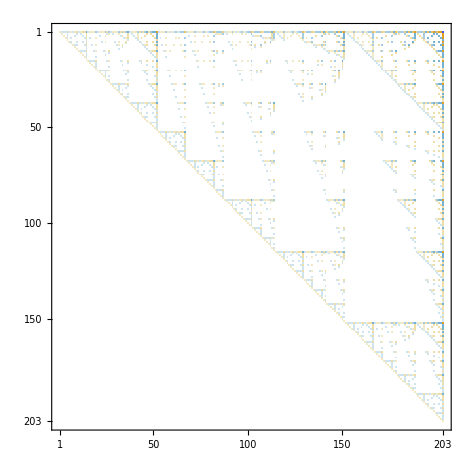

```mathematica
With[
{all=allGraphs6,
null=allGraphs6NullAtomKeys,
full=allGraphs6AtomKeys
},
Table[
Table[
With[
{form = all[k,"colofour"]},
Coefficient[form, all[m,"colofour"]]
],
{m, full//Sort}
]
,{k,null//Sort}]//Inverse//MatrixPlot
]
```

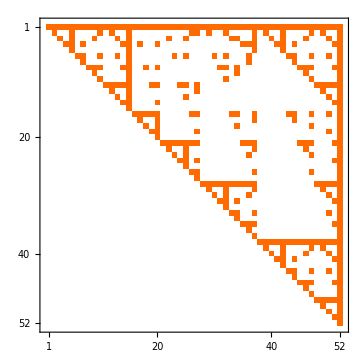

```mathematica
With[
{all=allGraphs5,
null=allGraphs5NullAtomKeys,
full=allGraphs5AtomKeys
},
Table[
Table[
With[
{form = all[k,"colofourrealnull"]},
Coefficient[form, all[m,"colofourrealnull"]]
],
{m, null//Sort}
]
,{k,full//Sort}]//Inverse//MatrixPlot
]
```

```mathematica
TraditionalForm[Sum[StirlingS2[n,k]2^ Binomial[k,2],{k,1,n}]]
```

∑_(k=1)^n 2^(1/2 (k-1) k) nk